## Q2

## b)

## Importing data for 200^2 grid points

```mathematica
data[200]=Table[Import["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR510\\HW3\\output_00"<>If[i<10,"0",""]<>ToString[i]<>".txt","Data"],{i,0,11}];
dx=1/200.;
dy=1/200.;
Nx=200;
Ny=200;
dt=.01;
```

### Defining column names

```mathematica
iZ=1;jZ=2; rhoZ=3;pZ=4;ErhoZ=5; uxZ=6;uyZ=7;
```

## c)

## Colormaps

### Pressure

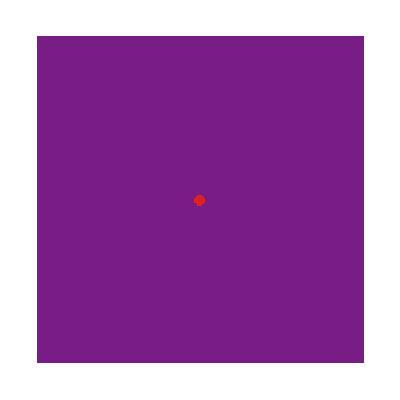
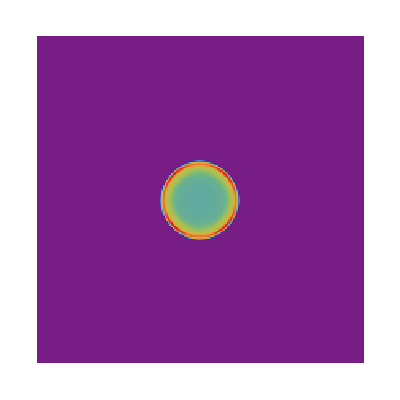
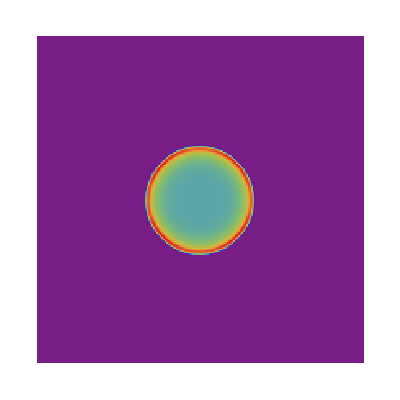
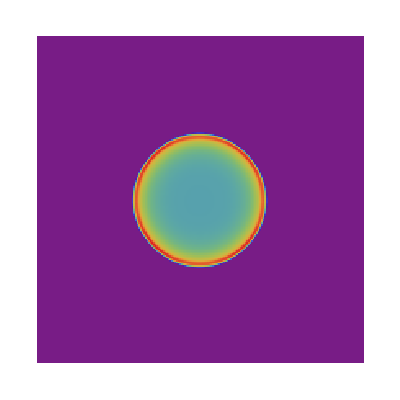
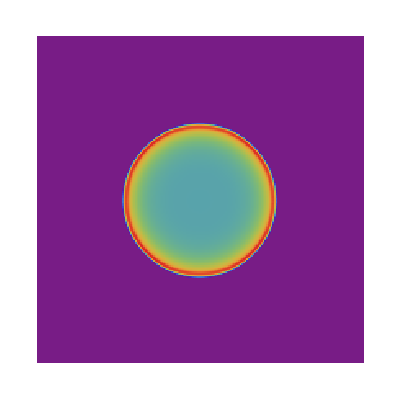
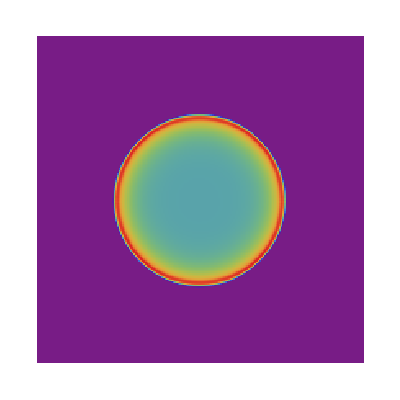
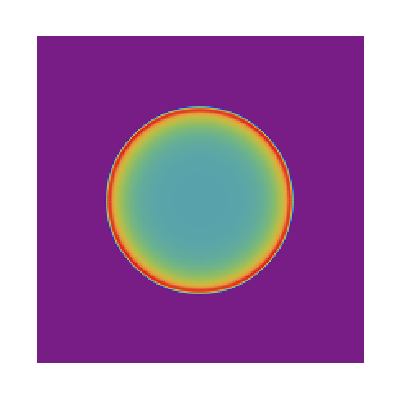
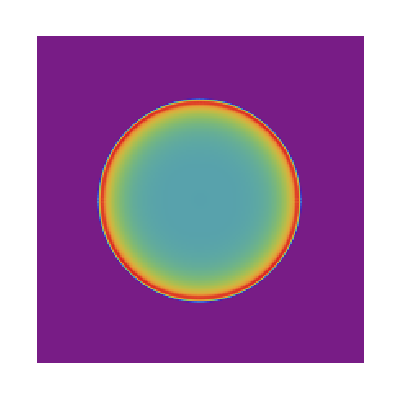

```mathematica
Table[ArrayPlot[Reverse@Partition[data[200]⟦i⟧⟦All,pZ⟧,Nx],ImageSize->Tiny,ColorFunction->"Rainbow"],{i,1,11}]//Row
```

### Density

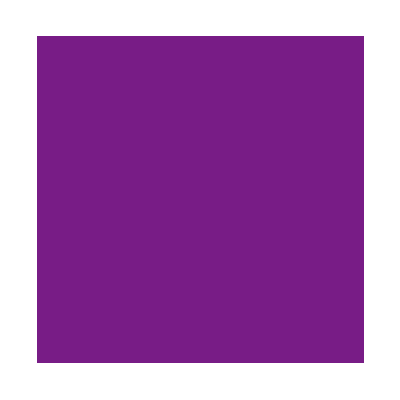
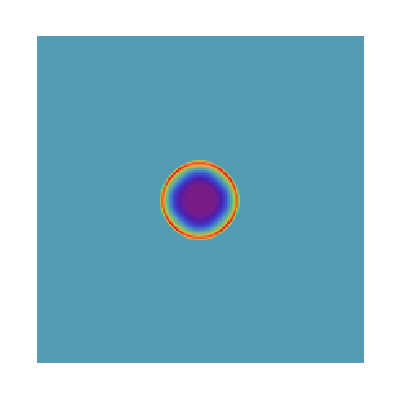
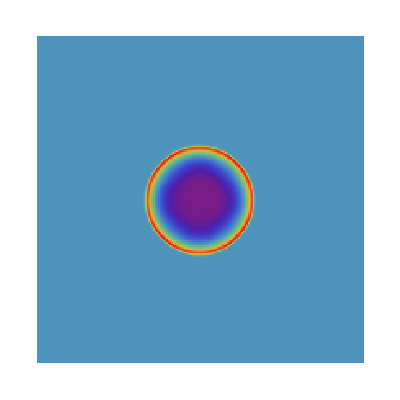
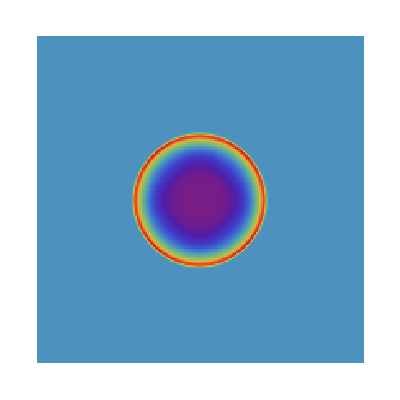
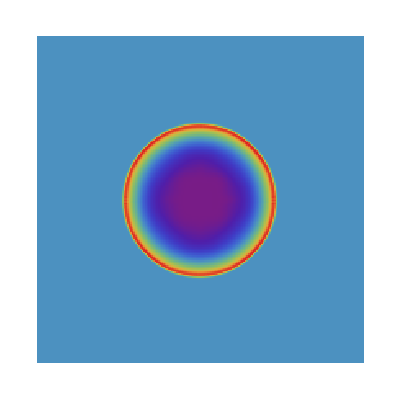
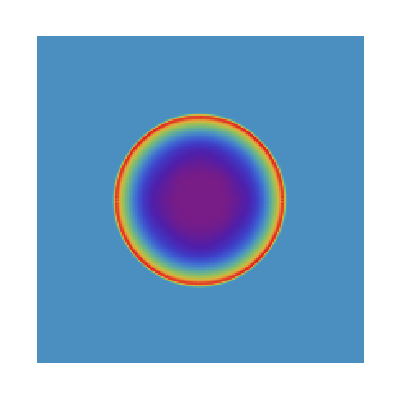
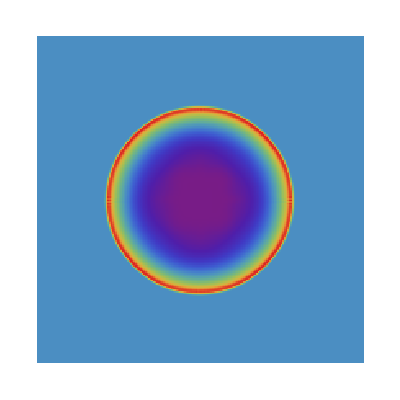
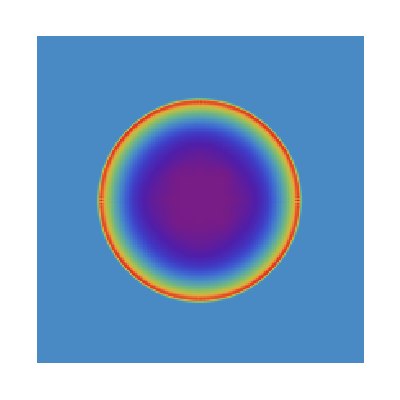

```mathematica
Table[ArrayPlot[Reverse@Partition[data[200]⟦i⟧⟦All,rhoZ⟧,Nx],ImageSize->Tiny,ColorFunction->"Rainbow"],{i,1,11}]//Row
```

## Radial averages

### Grouping zones by radial distance

```mathematica
grid=GatherBy[Tuples[{Range[Nx],Range[Ny]}],Floor [ Norm [#-{Nx/2+.5,Ny/2+.5} ]]&];
```

### Averaging density over radial bins

```mathematica
rhoAv=Table[Reverse[Mean/@(Extract[Transpose[Partition[data[200]⟦i⟧⟦All,rhoZ⟧,Nx]],#]&/@grid)],{i,11}];
```

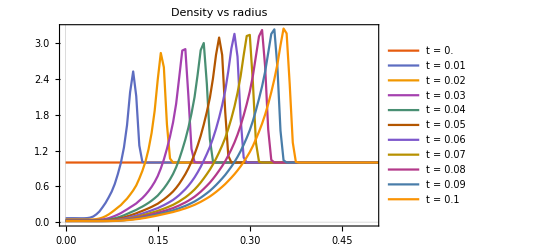

```mathematica
ListLinePlot[Table[Transpose[{Table[j*dx,{j,0,Length[rhoAv⟦i⟧]-1}],rhoAv⟦i⟧}],{i,11}],Frame->True,PlotTheme->"Scientific",PlotRange->{{0,.5},All},PlotLegends->Table["t = "<>ToString[dt i],{i,0,10}],PlotLabel->"Density vs radius"]
```

### Averaging pressure over radial bins

```mathematica
p0Av=Table[Reverse[Mean/@(Extract[Transpose[Partition[data[200]⟦i⟧⟦All,pZ⟧,Nx]],#]&/@grid)],{i,11}];
```

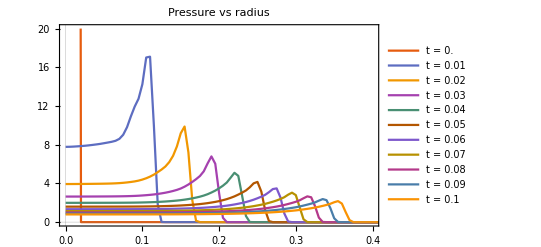

```mathematica
ListLinePlot[Table[Transpose[{Table[j*.005,{j,0,Length[p0Av⟦i⟧]-1}],p0Av⟦i⟧}],{i,11}],PlotRange->{{0,.4},{0,20}},Frame->True,PlotTheme->"Scientific",PlotLegends->Table["t = "<>ToString[.01i],{i,0,10}],PlotLabel->"Pressure vs radius"]
```

The shock positions seem to be correct because the peaks in the pressure profiles match exactly with the peaks in the density profiles.

### Averaging radial velocity over radial bins

```mathematica
Vr0=Table[-(#⟦1⟧*(dx*Nx/2-dx#⟦3⟧)+#⟦2⟧*(dy*Ny/2-dy#⟦4⟧))/Sqrt[$MachineEpsilon+(dx*Nx/2.-dx#⟦3⟧)^2+(dy*Ny/2.-dy#⟦4⟧)^2]&[Transpose[Partition[data[200]⟦i⟧⟦All,#⟧,Nx]]&/@{uxZ,uyZ,iZ,jZ}],{i,11}];
```

```mathematica
Vr0Av=Table[Reverse[Mean/@(Extract[Vr0⟦i⟧,#]&/@grid)],{i,11}];
```

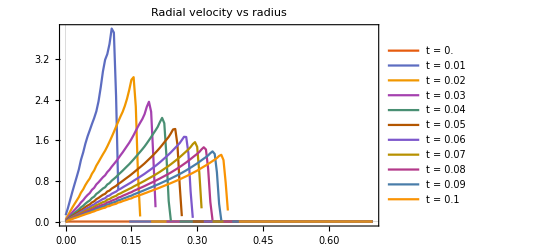

```mathematica
ListLinePlot[Table[Transpose[{Table[j*dx,{j,0,Length[Vr0Av⟦i⟧]-1}],Vr0Av⟦i⟧}],{i,11}],PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Table["t = "<>ToString[dt i],{i,0,10}],PlotLabel->"Radial velocity vs radius"]
```

### Averaging transverse velocity over radial bins

Finding magnitude of velocity at each zone:

```mathematica
Vt0=Table[-(-#⟦1⟧*(dy*Ny/2-dy#⟦4⟧)+#⟦2⟧*(dx*Nx/2-dx#⟦3⟧))/Sqrt[$MachineEpsilon+(dx*Nx/2.-dx#⟦3⟧)^2+(dy*Ny/2.-dy#⟦4⟧)^2]&[Transpose[Partition[data[200]⟦i⟧⟦All,#⟧,Nx]]&/@{uxZ,uyZ,iZ,jZ}],{i,11}];
```

```mathematica
Vt0Av=Table[Reverse[Mean/@(Extract[Vt0⟦i⟧,#]&/@grid)],{i,11}];
```

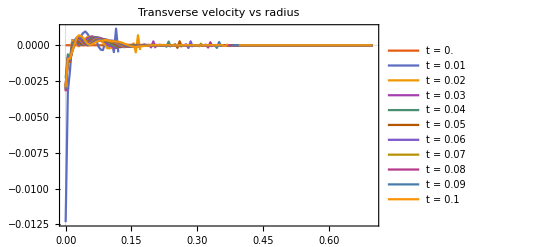

```mathematica
ListLinePlot[Table[Transpose[{Table[j*dx,{j,0,Length[Vt0Av⟦i⟧]-1}],Vt0Av⟦i⟧}],{i,11}],PlotRange->All,Frame->True,PlotTheme->"Scientific",PlotLegends->Table["t = "<>ToString[dt i],{i,0,10}],PlotLabel->"Transverse velocity vs radius"]
```

### Scatter plot of transverse velocity vs radius at t = .1

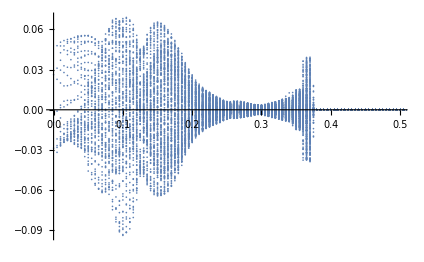

```mathematica
With[{temp=Reverse[(Extract[Vt0⟦-1⟧,#]&/@grid)]},ListPlot[Flatten[Table[{dx (j-1),temp[[j,i]]},{j,1,Length[temp]},{i,1,Length[temp[[j]]]}],1],PlotRange->{{0,.5},All}]]
```

It can be seen that on average the transverse velocity is approximately zero as expected from the plot of the radial average. The scatter about the mean value can be reduced by choosing the initial perturbation to be a disk covering a few zones (about 3.5 zones radially) so as to minimize effects due to the square shapes of the zones.

### Scatter plot of radial velocity vs radius at t = .1

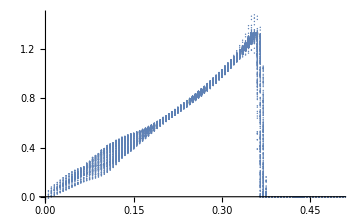

```mathematica
With[{temp=Reverse[(Extract[Vr0⟦-1⟧,#]&/@grid)]},ListPlot[Flatten[Table[{dx (j-1),temp[[j,i]]},{j,1,Length[temp]},{i,1,Length[temp[[j]]]}],1],PlotRange->{{0,.5},All}]]
```

### Scatter plot of pressure vs radius at t = .1

```mathematica
With[{temp=Reverse[(Extract[Transpose[Partition[data[200]⟦-1⟧⟦All,pZ⟧,Nx]],#]&/@grid)]},ListPlot[Flatten[Table[{dx (j-1),temp[[j,i]]},{j,1,Length[temp]},{i,1,Length[temp[[j]]]}],1],PlotRange->{{0,.5},All}]]
```

-Graphics-

### Scatter plot of density vs radius at t = .1

```mathematica
With[{temp=Reverse[(Extract[Transpose[Partition[data[200]⟦-1⟧⟦All,rhoZ⟧,Nx]],#]&/@grid)]},ListPlot[Flatten[Table[{dx (j-1),temp[[j,i]]},{j,1,Length[temp]},{i,1,Length[temp[[j]]]}],1],PlotRange->{{0,.5},All}]]
```

-Graphics-

## d)

## Finding shock front position from pressure profile

We can find the shock front zone number by calculating the location of the first maxima which we encounter as we move from the boundaries to the center.

```mathematica
shF=Transpose[{Range[0,.1,.01],.005((FindPeaks/@p0Av)⟦;;11,-1,1⟧-1)}];
```

### Log-log plot of radial position of the shock front vs time

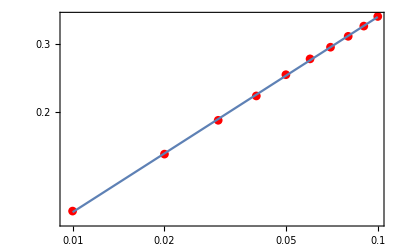

```mathematica
Show[ListLogLogPlot[shF,Frame->True,PlotStyle->Red,PlotMarkers->Automatic],LogLogPlot[E^fsH[Log[t]],{t,0.01,.1}]]
```

### Best fit line to the log-log plot

```mathematica
fsH[x_]=Fit[Log@shF⟦2;;-1⟧,{1,x},x]
```

0.136999+0.510512 x

Therefore the position of the shock front scales approximately as t^0.5

## e)

## PLM method

### Importing analytic solution for pressure

```mathematica
sol=Import["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR510\\HW3\\hydro\\sedov_analytic_512.txt","Data"]//.{}->Sequence[];
```

### Computing interpolating function of the analytic solution

```mathematica
fA=ListInterpolation[Transpose[Partition[sol⟦All,pZ⟧,512]],{{0,1},{0,1}}];
```

### Importing data for different grid sizes

```mathematica
Do[dataP[j]=Import["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR510\\HW3\\hydro\\hydro"<>ToString[j]<>"\\output_0011.txt","Data"],{j,{32,64,100,200,400,512}}];
```

### Computing interpolating functions of pressure for different grid sizes

```mathematica
Table[interp[i]=ListInterpolation[Transpose[Partition[dataP[i]⟦All,pZ⟧,i]],{{0,1},{0,1}}],{i,{32,64,100,200,400,512}}];
```

### Computing L2 norm of the difference between numerical solutions and analytic solution for different grid sizes

```mathematica
L2PLM=Transpose[{#,Function[g,StandardDeviation[(fA[#1,#2]-interp[g][#1,#2])&@@@Tuples[Range[0,1,1./512],2]]]/@#}]&@{32,64,100,200,400,512};
```

### Log-log plot of error vs grid size

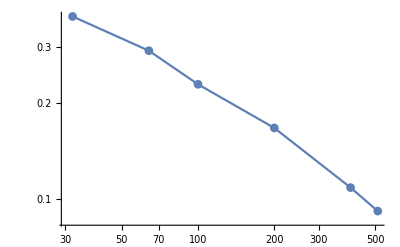

```mathematica
ListLogLogPlot[L2PLM,Joined->True,PlotMarkers->Automatic]
```

## Godunov method

### Importing data for different grid sizes

```mathematica
Do[dataG[j]=Import["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR510\\HW3\\hydro\\hydroG"<>ToString[j]<>"\\output_0011.txt","Data"],{j,{32,64,100,200,400,512}}];
```

### Creating interpolating functions of pressure for different grid sizes

```mathematica
Table[interpG[i]=ListInterpolation[Transpose[Partition[dataG[i]⟦All,pZ⟧,i]],{{0,1},{0,1}}],{i,{32,64,100,200,400,512}}];
```

### Computing L2 norm of the difference between numerical solutions and analytic solution for different grid sizes

```mathematica
L2GDV=Transpose[{#,Function[g,StandardDeviation[(fA[#1,#2]-interpG[g][#1,#2])&@@@Tuples[Range[0,1,1./512],2]]]/@#}]&@{32,64,100,200,400,512};
```

### Log-log plot of error vs grid size

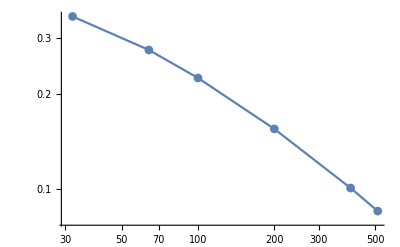

```mathematica
ListLogLogPlot[L2GDV,Joined->True,PlotMarkers->Automatic]
```

## f)

## Comparison of the two methods

### Log-log plot of error vs grid size

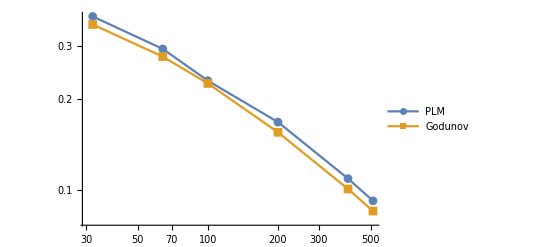

```mathematica
ListLogLogPlot[{L2PLM,L2GDV},Joined->True,PlotMarkers->Automatic,PlotLegends->{"PLM","Godunov"}]
```

Without excluding the zones at the shock, we can see that both methods show almost the same rate of convergence (with the godunov method being slightly more accurate). It is expected that after excluding the regions containing the shock, the godunov method would show a faster rate of convergence.